## Finite Spherical Quantum Well

#### Energy Eigenvalues:

At l = 0;

```mathematica
<<PhysicalConstants`     (* Constants Package *)
```

```mathematica
clear[z0];
z0=8;
besselD[l_]=D[SphericalBesselJ[l,Sqrt[z0^2+z^2]],z];
hankelD[l_]=D[SphericalHankelH1[l,z],z]; 
transleft=Sqrt[((z0/z)^2-1)];
transright[l_]= (SphericalBesselJ[l,Sqrt[z0^2+z^2]]/besselD[l])*(Abs[hankelD[l]]/Abs[SphericalHankelH1[l,z]]);
```

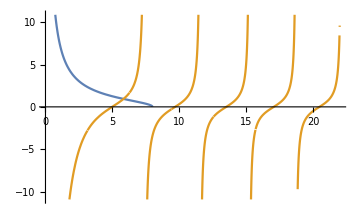
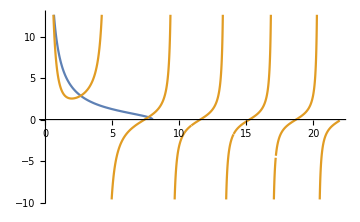
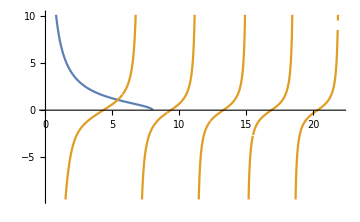
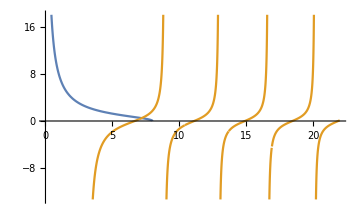

```mathematica
Table[Plot[{transleft,transright[n]},{z,0,22}, PlotRange->Automatic,ImageSize-> Medium],{n,0,3}]
```

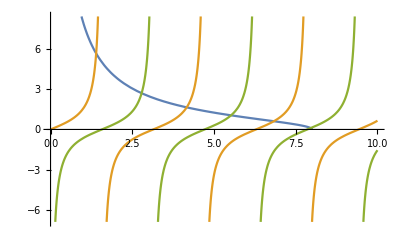

```mathematica
Plot[{Sqrt[(8/z)^2-1],Tan[z],-Cot[z]}, {z,0,10}]
```